```mathematica
<<SciDraw`
```

𝒮𝒸𝒾𝒟𝓇𝒶𝓌: Publication–quality scientific figures with Mathematica
M. A. Caprio, University of Notre Dame
Version 0.0.3 (February 20, 2014)
View color paletteVisit home page  -Graphics-

```mathematica
(*Input Data from International Prizepool Tracker*)
TI5={{0,1.6},{1,3.527102},{2,4.551752},{3,5.131860},{4,5.599591},{5,5.980978},{6,6.334299},{7,6.621347},{8,6.925868},{9,7.195787},{10,7.385511},{11,7.557339},{12,7.705689},{13,7.857829},{14,7.993835},{15,8.149170},{16,8.286128},{17,8.390569},{18,8.486207},{19,8.574268},{20,8.649109},{21,8.721204},{22,8.828932},{23,8.918565},{24,8.990314},{25,9.065465},{26,9.138751},{27,9.205726}}
TI5Imm1={{28,9.471543},{29,9.849911},{30,10.061310},{31,10.222959},{32,10.367032},{33,10.489378},{34,10.596326}}
TI5Cache={{35,11.054546},{36,11.921890},{37,12.299289},{38,12.553290},{39,12.769750},{40,12.962955},{41,13.135147},{42,13.277064},{43,13.430689},{44,13.557865},{45,13.672518},{46,13.779775},{47,13.880366},{48,13.960703},{49,14.048013},{50,14.148485},{51,14.238011},{52,14.316457},{53,14.394469},{54,14.466326},{55,14.533884}}
```

{{0,1.6},{1,3.5271},{2,4.55175},{3,5.13186},{4,5.59959},{5,5.98098},{6,6.3343},{7,6.62135},{8,6.92587},{9,7.19579},{10,7.38551},{11,7.55734},{12,7.70569},{13,7.85783},{14,7.99384},{15,8.14917},{16,8.28613},{17,8.39057},{18,8.48621},{19,8.57427},{20,8.64911},{21,8.7212},{22,8.82893},{23,8.91857},{24,8.99031},{25,9.06547},{26,9.13875},{27,9.20573}}

{{28,9.47154},{29,9.84991},{30,10.0613},{31,10.223},{32,10.367},{33,10.4894},{34,10.5963}}

{{35,11.0545},{36,11.9219},{37,12.2993},{38,12.5533},{39,12.7698},{40,12.963},{41,13.1351},{42,13.2771},{43,13.4307},{44,13.5579},{45,13.6725},{46,13.7798},{47,13.8804},{48,13.9607},{49,14.048},{50,14.1485},{51,14.238},{52,14.3165},{53,14.3945},{54,14.4663},{55,14.5339}}

```mathematica
(*This Notebook is designed to act as a rough estimator for the Dota 2 International Tournament Prizepool*)
(*Written early 2015, quickly.*)
```

```mathematica
func=(a*Log[d*x+1]+1.6)
ImmortalShiftFunc=a*Log[x-c]+b
ImmortalFunc2=a*Log[x-20.875]+b
ImmortalFunc3=a*Log[x-20.875]+b
ImmortalFunc4=a*Log[x-20.875]+b
ImmortalFunc5=a*Log[x-20.875]+b
```

1.6+a Log[1+d x]

b+a Log[-c+x]

b+a Log[-20.875+x]

b+a Log[-20.875+x]

b+a Log[-20.875+x]

«1 more identical outputs»

```mathematica
TI5Fit=FindFit[TI5,func,{a,b,c,d},x]
```

{a→2.01083,b→1.,c→1.,d→1.62729}

```mathematica
TI5func=func/.%
```

1.6+2.01083 Log[1+1.62729 x]

```mathematica
TI5Imm1Fit=FindFit[TI5Imm1,TI5func+ImmortalShiftFunc/.c->26.875,{a,b,c,d},x]
```

{a→0.397,b→0.130259,c→0.,d→0.}

```mathematica
TI5Imm1func=TI5func+ImmortalShiftFunc/.c->26.875/.%
```

1.73026+0.397 Log[-26.875+x]+2.01083 Log[1+1.62729 x]

```mathematica
TI5Imm2func=TI5func+ImmortalShiftFunc/.{c->34.875,b->1.2,a->0.41412250572074694}
TI5Imm3func=TI5func+ImmortalShiftFunc/.{c->41.875,b->1.4,a->0.41412250572074694}
TI5Imm4func=TI5func+ImmortalShiftFunc/.{c->48.875,b->1.6,a->0.41412250572074694}
```

2.8+0.414123 Log[-34.875+x]+2.01083 Log[1+1.62729 x]

3.+0.414123 Log[-41.875+x]+2.01083 Log[1+1.62729 x]

3.2+0.414123 Log[-48.875+x]+2.01083 Log[1+1.62729 x]

```mathematica
TI5CacheFit=FindFit[TI5Cache,TI5Imm1func+ImmortalShiftFunc/.c->33.875,{a,b,c,d},x]
```

{a→0.642649,b→0.546775,c→0.,d→0.}

```mathematica
TI5CacheFunc=TI5Imm1func+ImmortalShiftFunc/.c->33.875/.%
```

2.27703+0.642649 Log[-33.875+x]+0.397 Log[-26.875+x]+2.01083 Log[1+1.62729 x]

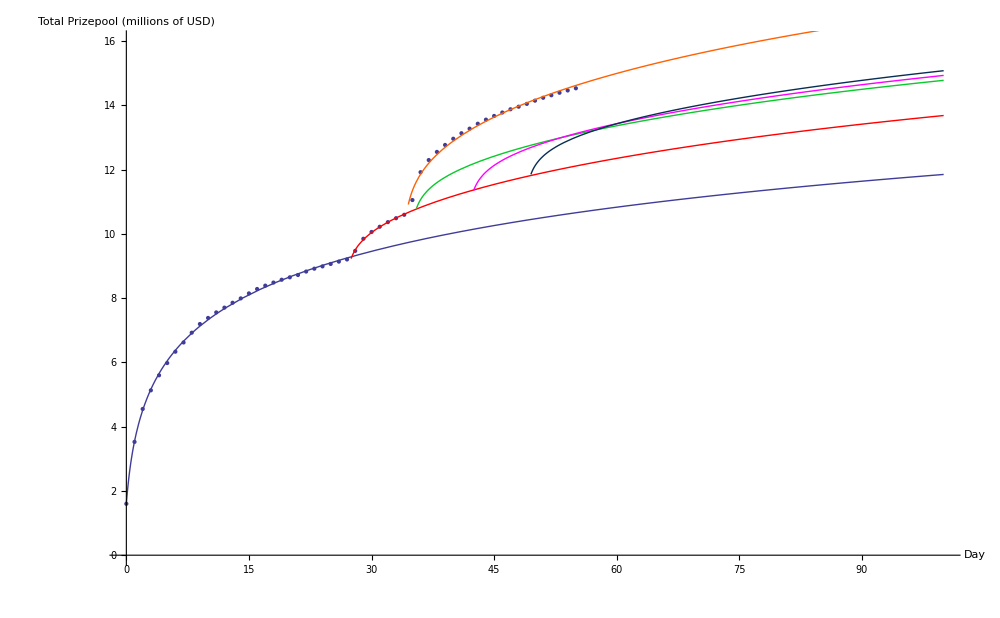

```mathematica
TI5DataPlot=ListPlot[TI5,Joined->False,LabelStyle->Directive[Black,Medium],AxesLabel->{"Day","Total Prizepool (millions of USD)"},ImageSize->200*{5,3},PlotRange->{{0,100},{0,16}}];
TI5FuncPlot=Plot[TI5func,{x,0,100}];
TI5Imm1DataPlot=ListPlot[TI5Imm1,Joined->False,LabelStyle->Directive[Black,Medium],AxesLabel->{"Day","Total Prizepool (millions of USD)"},ImageSize->200*{5,3},PlotRange->{{0,100},{0,16}}];
TI5CacheDataPlot=ListPlot[TI5Cache,Joined->False,LabelStyle->Directive[Black,Medium],AxesLabel->{"Day","Total Prizepool (millions of USD)"},ImageSize->200*{5,3},PlotRange->{{0,100},{0,16}}];
TI5Imm1FuncPlot=Plot[TI5Imm1func,{x,27.5,100},PlotStyle->Red];
TI5Imm2FuncPlot=Plot[TI5Imm2func,{x,35.5,100},PlotStyle->PermanentGreen];
TI5Imm3FuncPlot=Plot[TI5Imm3func,{x,42.5,100},PlotStyle->Magenta];
TI5Imm4FuncPlot=Plot[TI5Imm4func,{x,49.5,100},PlotStyle->Indigo];
TI5CacheFuncPlot=Plot[TI5CacheFunc,{x,34.5,100},PlotStyle->CadmiumOrange];
Show[{TI5DataPlot,TI5FuncPlot,TI5Imm1DataPlot,TI5Imm1FuncPlot,TI5Imm2FuncPlot,TI5Imm3FuncPlot,TI5Imm4FuncPlot,TI5CacheDataPlot,TI5CacheFuncPlot}]
```

```mathematica
TI5FinalPool=TI5func/.x->100
TI5Imm2func/.x->100
TI5Imm3func/.x->100
TI5Imm4func/.x->100
```

11.8516

14.7811

14.934

15.0809

```mathematica
Variance0=0;
Variance1=Extract[TI5,{1,2}]-TI5func/.x->0;
Variance2=Extract[TI5,{2,2}]-TI5func/.x->1;
Variance3=Extract[TI5,{3,2}]-TI5func/.x->2;
Variance4=Extract[TI5,{4,2}]-TI5func/.x->3;
Variance5=Extract[TI5,{5,2}]-TI5func/.x->4;
Variance6=Extract[TI5,{6,2}]-TI5func/.x->5;
Variance7=Extract[TI5,{7,2}]-TI5func/.x->6;
Variance8=Extract[TI5,{8,2}]-TI5func/.x->7;
Variance9=Extract[TI5,{9,2}]-TI5func/.x->8;
Variance10=Extract[TI5,{10,2}]-TI5func/.x->9;
Variance11=Extract[TI5,{11,2}]-TI5func/.x->10;
Variance12=Extract[TI5,{12,2}]-TI5func/.x->11;
Variance13=Extract[TI5,{13,2}]-TI5func/.x->12;
Variance14=Extract[TI5,{14,2}]-TI5func/.x->13;
Variance15=Extract[TI5,{15,2}]-TI5func/.x->14;
Variance16=Extract[TI5,{16,2}]-TI5func/.x->15;
Variance17=Extract[TI5,{17,2}]-TI5func/.x->16;
Variance18=Extract[TI5,{18,2}]-TI5func/.x->17;
Variance19=Extract[TI5,{19,2}]-TI5func/.x->18;
Variance20=Extract[TI5,{20,2}]-TI5func/.x->19;
Variance21=Extract[TI5,{21,2}]-TI5func/.x->20;
Variance22=Extract[TI5,{22,2}]-TI5func/.x->21;
Variance23=Extract[TI5,{23,2}]-TI5func/.x->22;
Variance24=Extract[TI5,{24,2}]-TI5func/.x->23;
Variance25=Extract[TI5,{25,2}]-TI5func/.x->24;
Variance26=Extract[TI5,{26,2}]-TI5func/.x->25;
Variance27=Extract[TI5,{27,2}]-TI5func/.x->26;
Variance28=Extract[TI5Imm1,{1,2}]-TI5Imm1func/.x->28;
Variance29=Extract[TI5Imm1,{2,2}]-TI5Imm1func/.x->29;
Variance30=Extract[TI5Imm1,{3,2}]-TI5Imm1func/.x->30;
Variance31=Extract[TI5Imm1,{4,2}]-TI5Imm1func/.x->31;
Variance32=Extract[TI5Imm1,{5,2}]-TI5Imm1func/.x->32;
Variance33=Extract[TI5Imm1,{6,2}]-TI5Imm1func/.x->33;
Variance34=Extract[TI5Imm1,{7,2}]-TI5Imm1func/.x->34;
```

{{28,-0.0287283},{29,0.0280792},{30,0.0195913},{31,0.00638818},{32,0.00166716},{33,-0.00747952},{34,-0.019518}}

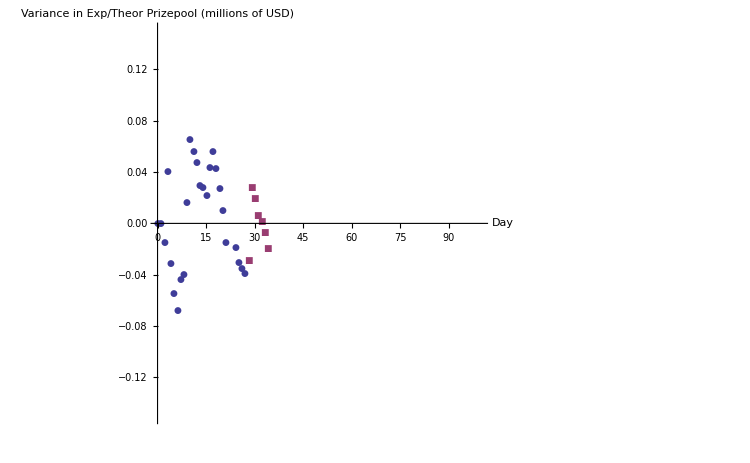

```mathematica
VarianceArray={{0,Variance0},{1,Variance1},{2,Variance2},{3,Variance3},{4,Variance4},{5,Variance5},{6,Variance6},{7,Variance7},{8,Variance8},{9,Variance9},{10,Variance10},{11,Variance11},{12,Variance12},{13,Variance13},{14,Variance14},{15,Variance15},{16,Variance16},{17,Variance17},{18,Variance18},{19,Variance19},{20,Variance20},{21,Variance21},{22,Variance22}{23,Variance23},{24,Variance24},{25,Variance25},{26,Variance26},{27,Variance27}};
VarianceArrayImm1={{28,Variance28},{29,Variance29},{30,Variance30},{31,Variance31},{32,Variance32},{33,Variance33},{34,Variance34}}
ListPlot[{VarianceArray,VarianceArrayImm1},Joined->False,LabelStyle->Directive[Black,Medium],AxesLabel->{"Day","Variance in Exp/Theor Prizepool (millions of USD)"},ImageSize->150*{5,3},PlotRange->{{0,100},{-0.15,0.15}},PlotMarkers->Automatic]
```

{a→1.9695,b→1.,c→1.,d→0.778815}

1.6+1.9695 Log[1+0.778815 x]

{a→0.269064,b→0.521153,c→0.,d→0.}

2.12115+1.9695 Log[1+0.778815 x]+0.269064 Log[-20.875+x]

{a→-0.34227,b→0.922985,c→0.,d→0.}

3.04414+1.9695 Log[1+0.778815 x]-0.073206 Log[-20.875+x]

{a→0.471967,b→-1.59483,c→0.,d→0.}

1.44931+1.9695 Log[1+0.778815 x]+0.398761 Log[-20.875+x]

{a→-0.437122,b→1.64938,c→0.,d→0.}

3.09869+1.9695 Log[1+0.778815 x]-0.0383604 Log[-20.875+x]

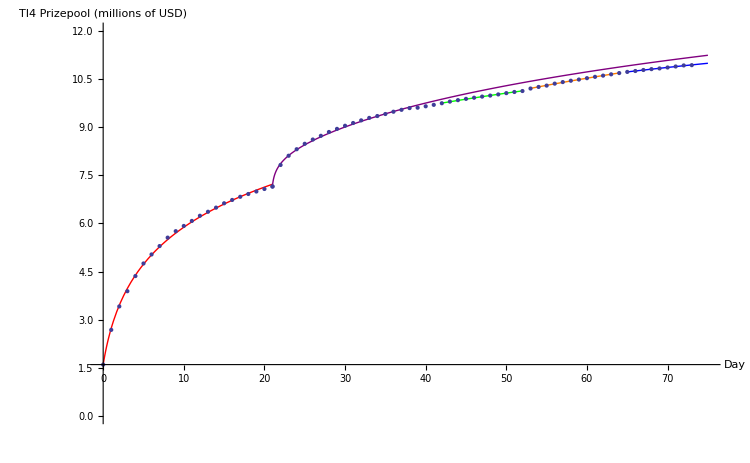

```mathematica
TI4Period1={{0,1.6},{1,2.682056},{2,3.412386},{3,3.887103},{4,4.359369},{5,4.75109},{6,5.032238},{7,5.293739},{8,5.556659},{9,5.757481},{10,5.920247},{11,6.077071},{12,6.237971},{13,6.362555},{14,6.491085},{15,6.626895},{16,6.730669},{17,6.829365},{18,6.916236},{19,6.993768},{20,7.072585},{21,7.149563}};
TI4Period2={{21,7.149563},{22,7.820603},{23,8.108294},{24,8.311263},{25,8.480723},{26,8.613332},{27,8.729162},{28,8.84857},{29,8.945598},{30,9.042588},{31,9.128411},{32,9.210697},{33,9.287343},{34,9.345867},{35,9.40875},{36,9.479952},{37,9.53958},{38,9.593305},{39,9.605399},{40,9.649285}};
TI4Period3={{41,9.69444},{42,9.744198},{43,9.795226},{44,9.84048},{45,9.880467},{46,9.916212},{47,9.951433},{48,9.983165},{49,10.019255},{50,10.059037},{51,10.095225},{52,10.124692}};
TI4Period4={{53,10.202874},{54,10.252018},{55,10.294087},{56,10.355167},{57,10.40384},{58,10.445503},{59,10.482631},{60,10.52542},{61,10.566884},{62,10.604889},{63,10.645383},{64,10.68461}};
TI4Period5={{65,10.720393},{66,10.748667},{67,10.780082},{68,10.807186},{69,10.829017},{70,10.858302},{71,10.889695},{72,10.922374},{73,10.931105}};
TI4P1Plot=ListPlot[TI4Period1,Joined->False,LabelStyle->Directive[Black,Medium],AxesLabel->{"Day","Variance in Exp/Theor Prizepool (millions of USD)"},ImageSize->150*{5,3},PlotRange->{{0,100},{0,16}}];
TI4P2Plot=ListPlot[TI4Period2,Joined->False,LabelStyle->Directive[Black,Medium],AxesLabel->{"Day","Variance in Exp/Theor Prizepool (millions of USD)"},ImageSize->150*{5,3},PlotRange->{{0,100},{0,16}}];
TI4P3Plot=ListPlot[TI4Period3,Joined->False,LabelStyle->Directive[Black,Medium],AxesLabel->{"Day","Variance in Exp/Theor Prizepool (millions of USD)"},ImageSize->150*{5,3},PlotRange->{{0,100},{0,16}}];
TI4P4Plot=ListPlot[TI4Period4,Joined->False,LabelStyle->Directive[Black,Medium],AxesLabel->{"Day","Variance in Exp/Theor Prizepool (millions of USD)"},ImageSize->150*{5,3},PlotRange->{{0,100},{0,16}}];
TI4P5Plot=ListPlot[TI4Period5,Joined->False,LabelStyle->Directive[Black,Medium],AxesLabel->{"Day","Variance in Exp/Theor Prizepool (millions of USD)"},ImageSize->150*{5,3},PlotRange->{{0,100},{0,16}}];
TI4Log1=FindFit[TI4Period1,func,{a,b,c,d},x]
TI4Fit1=func/.%
TI4Plot1=Plot[TI4Fit1,{x,0,21},PlotStyle->Red];
TI4Log2=FindFit[TI4Period2,(ImmortalFunc2)+TI4Fit1,{a,b,c,d},x]
TI4Fit2=(ImmortalFunc2)+TI4Fit1/.%
TI4Plot2=Plot[TI4Fit2,{x,21,75},PlotStyle->Purple];
TI4Log3=FindFit[TI4Period3,(ImmortalFunc3)+TI4Fit2,{a,b,c,d},x]
TI4Fit3=(ImmortalFunc3)+TI4Fit2/.%
TI4Plot3=Plot[TI4Fit3,{x,42,52},PlotStyle->Green];
TI4Log4=FindFit[TI4Period4,(ImmortalFunc4)+TI4Fit3,{a,b,c,d},x]
TI4Fit4=(ImmortalFunc4)+TI4Fit3/.%
TI4Plot4=Plot[TI4Fit4,{x,53,64},PlotStyle->Orange];
TI4Log5=FindFit[TI4Period5,(ImmortalFunc5)+TI4Fit4,{a,b,c,d},x]
TI4Fit5=(ImmortalFunc5)+TI4Fit4/.%
TI4Plot5=Plot[TI4Fit5,{x,65,75},PlotStyle->Blue];
Show[{TI4Plot1,TI4Plot2,TI4Plot3,TI4Plot4,TI4Plot5,TI4P1Plot,TI4P2Plot,TI4P3Plot,TI4P4Plot,TI4P5Plot},PlotRange->{0,12},ImageSize->150*{5,3},AxesLabel->{"Day","TI4 Prizepool (millions of USD)"}]
```

```mathematica
(* This is the ratio for Immortal 'strength' in modifying the logarithm *)
ImmortalRatio=0.16217
```

0.16217

```mathematica
TI4Fit1;
TI4Fit2;
TI4Fit2/TI4Fit1//FullSimplify;
Plot[{TI4Fit1,TI4Fit2},{x,0,100}];
```

```mathematica
TIProp=1.35228
TI5ImmProp=TIProp*ImmortalRatio
```

1.35228

0.219299

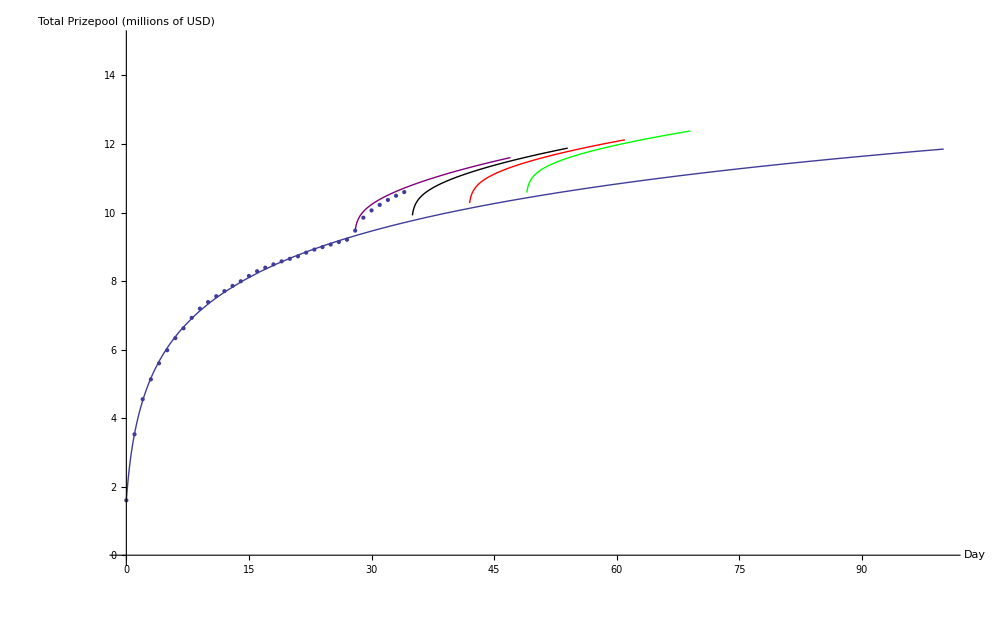

13.3514

```mathematica
TI5ImmortalExt1=TI5func+ImmortalShiftFunc/.{a->TI5ImmProp,b->0.60885,c->41.875};
TI5ImmortalExt2=TI5func+ImmortalShiftFunc/.{a->TI5ImmProp,b->0.60885,c->48.875};
TI5ImmortalExt3=TI5func+ImmortalShiftFunc/.{a->TI5ImmProp,b->0.60885,c->27.875};
TI5ImmortalExt4=TI5func+ImmortalShiftFunc/.{a->TI5ImmProp,b->0.60885,c->34.875};

TI5ImmortalPlot1=Plot[TI5ImmortalExt1,{x,42,61},PlotStyle->Red];
TI5ImmortalPlot2=Plot[TI5ImmortalExt2,{x,49,69},PlotStyle->Green];
TI5ImmortalPlot3=Plot[TI5ImmortalExt3,{x,28,47},PlotStyle->Purple];
TI5ImmortalPlot4=Plot[TI5ImmortalExt4,{x,35,54},PlotStyle->Black];

Show[{TI5DataPlot,TI5FuncPlot,TI5ImmortalPlot1,TI5ImmortalPlot2,TI5ImmortalPlot3,TI5ImmortalPlot4,TI5Imm1DataPlot},PlotRange->{{0,100},{0,15}}]
TI5ImmortalExt1/.x->100
```

```mathematica
TI5Immortal3Ext1=TI5ImmortalExt1+ImmortalShiftFunc/.{a->TI5ImmProp,b->0.60885,c->20.875}
TI5Immortal3Plot1=Plot[TI5Immortal3Ext1,{x,21,100},PlotStyle->Brown];
```

2.8177+0.219299 Log[-41.875+x]+0.219299 Log[-20.875+x]+2.01083 Log[1+1.62729 x]

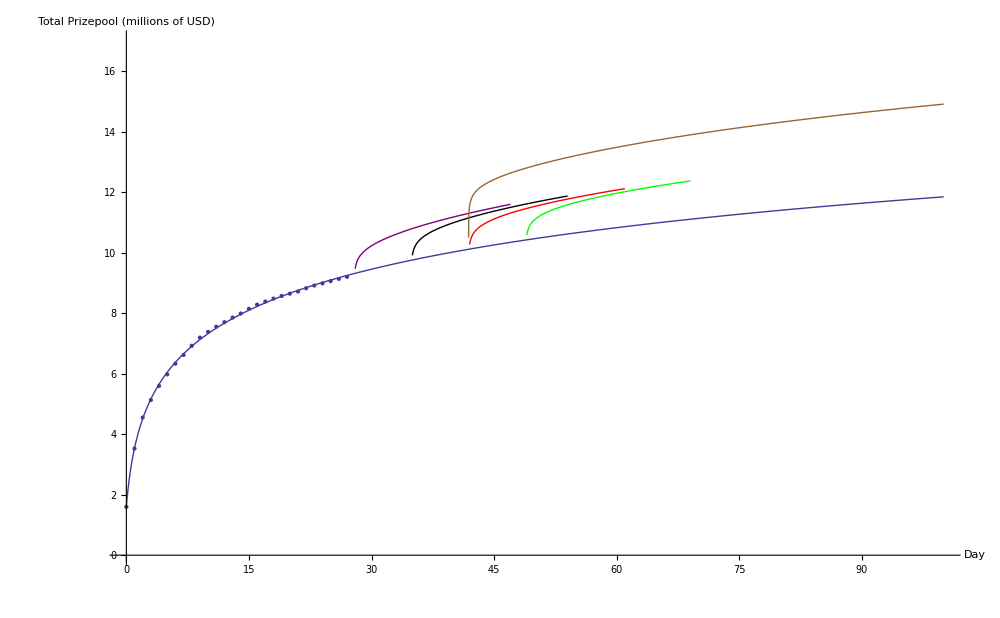

```mathematica
Show[{TI5DataPlot,TI5FuncPlot,TI5ImmortalPlot1,TI5ImmortalPlot2,TI5ImmortalPlot3,TI5ImmortalPlot4,TI5Immortal3Plot1},PlotRange->{{0,100},{0,17}}]
```

```mathematica
TI5Immortal3Ext1/.x->100
```

14.9188

```mathematica
TI5Imm3Func=TI5Imm1func+ImmortalShiftFunc
```

1.73026+b+0.397 Log[-26.875+x]+a Log[-c+x]+2.01083 Log[1+1.62729 x]

```mathematica
TI5Imm3Test1=TI5Imm3Func/.c->31.875
TI5Imm3Test2=TI5Imm3Func/.c->38.875
TI5Imm3Test3=TI5Imm3Func/.c->45.875
TI5Imm3Test4=TI5Imm3Func/.c->52.875
TI5Imm3Test5=TI5Imm3Func/.c->59.875
```

1.73026+b+a Log[-31.875+x]+0.397 Log[-26.875+x]+2.01083 Log[1+1.62729 x]

1.73026+b+a Log[-38.875+x]+0.397 Log[-26.875+x]+2.01083 Log[1+1.62729 x]

1.73026+b+a Log[-45.875+x]+0.397 Log[-26.875+x]+2.01083 Log[1+1.62729 x]

1.73026+b+a Log[-52.875+x]+0.397 Log[-26.875+x]+2.01083 Log[1+1.62729 x]

1.73026+b+a Log[-59.875+x]+0.397 Log[-26.875+x]+2.01083 Log[1+1.62729 x]

```mathematica
TestImm3=ImmortalShiftFunc/.{a->0.42587672973927887,b->0.11184337287616697,c->26.875,d->0.}
```

0.111843+0.425877 Log[-26.875+x]

```mathematica
Imm3Hump=0.211879
ImmHumpA=Imm3Hump*0.42587672973927887
ImmHumpB=Imm3Hump*0.60885
```

0.211879

0.0902343

0.129003

```mathematica
TI5Imm3Plot1=Plot[TestImm3,{x,32,100},PlotStyle->Green];
TI5Imm3Plot2=Plot[TI5Imm3Test2/.{a->ImmHumpA,b->ImmHumpB},{x,39,100},PlotStyle->Purple];
TI5Imm3Plot3=Plot[TI5Imm3Test3/.{a->ImmHumpA,b->ImmHumpB},{x,46,100},PlotStyle->Brown];
```

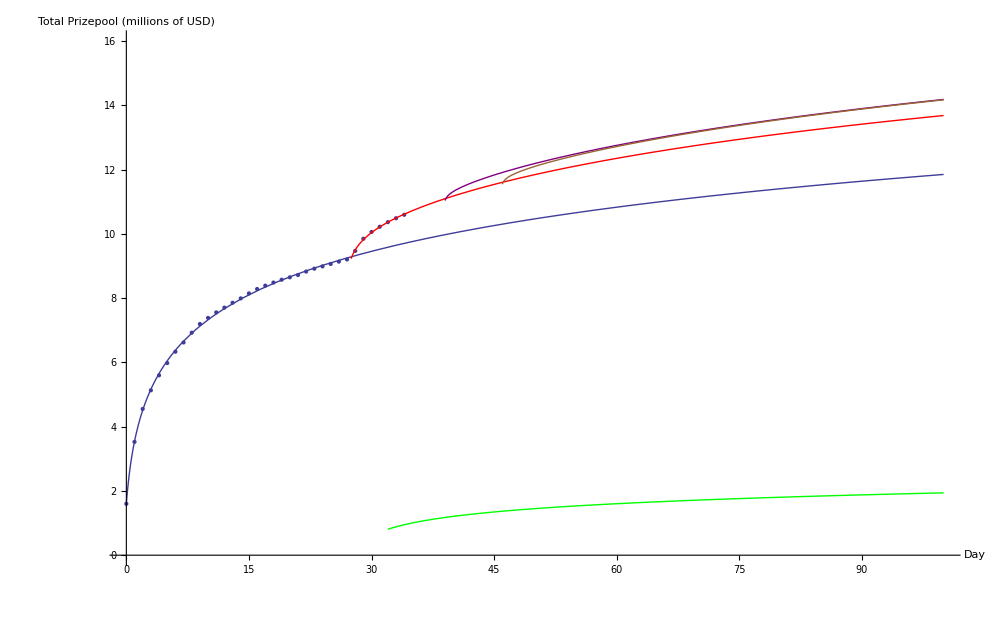

```mathematica
Show[{TI5DataPlot,TI5FuncPlot,TI5Imm1DataPlot,TI5Imm1FuncPlot,TI5Imm3Plot1,TI5Imm3Plot2,TI5Imm3Plot3}]
```

```mathematica
TI5Imm3Test1/.{a->ImmHumpA,b->ImmHumpB,x->100}
```

14.1958

```mathematica
ImmortalShiftFunc
```

b+a Log[-c+x]

```mathematica
s
```

s